```mathematica
(*
e[x]_here = e_1(x)_{Lagrangian approach};
v[x]_here = {v^1(x)}_{Lagrangian approach};
σ[x]_here  = σ(x)_{Lagrangian approach};
*)
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
ϵ[1]=1;
```

```mathematica
ass={ψ[x]∈Reals,ν[x]>0};
```

```mathematica
e[x_]:=ν[x]{Cos[ψ[x]],-Sin[ψ[x]]}
```

```mathematica
n[x_]:={-e[x][[2]],e[x][[1]]}/Norm[e[x]]
```

```mathematica
g[x_]:=Simplify[{{e[x].e[x]}},Assumptions->ass]
```

```mathematica
sqrtdetg[x_]:=Sqrt[Det[g[x]]]
```

```mathematica
gc[x_]:=Inverse[g[x]]
```

```mathematica
FullSimplify[{{-n'[x].e[x]}},Assumptions->ass]
```

{{-ν[x] ψ'[x]}}

```mathematica
b[x_]:={{-ν[x] ψ'[x]}}
```

```mathematica
1/2FullSimplify[Sum[gc[x][[i,j]]b[x][[j,i]],{i,1,1},{j,1,1}],Assumptions->ass]
```

-ψ'[x]/(2 ν[x])

```mathematica
H[x_]:=-ψ'[x]/(2 ν[x])
```

```mathematica
K[x_]:=0
```

```mathematica
Γ[x_]:=ResourceFunction["ChristoffelSymbol"][g[x],{x}] //FullSimplify
```

```mathematica
Γ[x]
```

{{{ν'[x]/ν[x]}}}

```mathematica
(* \Nabla_k f_i*)
```

```mathematica
Nablaf[f_][i_,k_][x_]:=Derivative[ϵ[k]][f[i]][x]-Sum[f[j][x] Γ[x][[j,i,k]],{j,1,1}]
```

```mathematica
(*\Nabla_k v^i*)
```

```mathematica
Nablav[f_][i_,k_][x_]:=Derivative[ϵ[k]][f[i]][x]+Sum[f[j][x] Γ[x][[i,j,k]],{j,1,1}]
```

```mathematica
dH[1][x_]:=H'[x]
```

```mathematica
FullSimplify[Sum[gc[x][[i,j]]Nablaf[dH][i,j][x],{i,1,1},{j,1,1}],Assumptions->ass]
```

(-3 ν'[x]^2 ψ'[x]+3 ν[x] ν'[x] ψ''[x]+ν[x] (ψ'[x] ν''[x]-ν[x] ψ^(3)[x]))/(2 ν[x]^5)

```mathematica
NabNabH[x_]:=(-3 ν'[x]^2 ψ'[x]+3 ν[x] ν'[x] ψ''[x]+ν[x] (ψ'[x] ν''[x]-ν[x] Derivative[3][ψ][x]))/(2 ν[x]^5)
```

```mathematica
(*sign*)
```

```mathematica
vv[1][x_]:=v[x]
```

```mathematica
FullSimplify[Nablav[vv][1,1][x],Assumptions->ass]
```

v'[x]+(v[x] ν'[x])/ν[x]

```mathematica
Nablaivi[x_]:=FullSimplify[Nablav[vv][1,1][x],Assumptions->ass]
```

```mathematica
(*eqψ=FullSimplify[{2 κ(2H[x](H[x]^2-K[x])+NabNabH[x])-2 σ[x]H[x]==0},Assumptions->ass]*)
```

```mathematica
(*eqX={X1'[x]==ν[x] Cos[ψ[x]],X2'[x]==-ν[x] Sin[ψ[x]]}*)
```

```mathematica
eqv=FullSimplify[ρ(v[x]Nablaivi[x]-2 v[x]w[x]b[x][[1,1]]-w[x] gc[x][[1,1]]w'[x])
-gc[x][[1,1]]σ'[x]
-2 η Nablak d^{ki}==0,Assumptions->ass];
eqσ=FullSimplify[Nablaivi[x]-2 H[x]w[x]==0,Assumptions->ass];
eqψ=FullSimplify[{ρ v[x](v[x]b[x][[1,1]]+w'[x])
-κ( - 2 NabNabH[x]-4H[x](H[x]^2-K[x]))
-2 σ[x]H[x]
- 2η( Nablaivi[x] gc[x][[1,1]]b[x][[1,1]]-2 w[x]*(2 H[x]^2-K[x]))==0},Assumptions->ass];
eqX={X1'[x]==ν[x] Cos[ψ[x]],X2'[x]==-ν[x] Sin[ψ[x]]};
```

```mathematica
eqψ
```

{ρ v[x] w'[x]+(ν[x] σ[x] ψ'[x]+2 η ν[x]^3 v'[x] ψ'[x]+2 η w[x] ψ'[x]^2+κ ψ'[x] ν''[x]+2 κ ν'[x] ψ''[x]-κ ν[x] ψ^(3)[x])/ν[x]^2==(ψ'[x] (2 ρ v[x]^2 ν[x]^4+κ (4 ν'[x]^2+ψ'[x]^2)))/(2 ν[x]^3)}

```mathematica
(*the ODEs above imply that v[x]=vc, and σ[x]=σc (independent of x), and because I am at steady state, it must be w[x]=0, thus I simplify the equations by setting *)
```

```mathematica
v[x_]:=vc
w[x_]:=0
σ[x_]:=σc
```

```mathematica
eqs=FullSimplify[Flatten[{eqψ,eqX}]]
```

{2 (vc^2 ρ-σc) ψ'[x]+κ ψ'[x]^3+2 κ ψ^(3)[x]==0,Cos[ψ[x]]==X1'[x],Sin[ψ[x]]+X2'[x]==0}

```mathematica
bcs={
ψ[xmin]==ψmin,ψ[xmax]==ψmax,ψ'[xmin]==ψpmin,
X1[xmin]==X1min,X2[xmin]==X2min};
```

```mathematica
(*parameters*)
```

```mathematica
κ=1;
ρ=1;
η=1;
xmin=1;
xmax=3;
vc=1;
σc=0;
ψmin=-1/2;
ψmax=2;
ψpmin=-1;
X1min=0;
X2min=0;
```

```mathematica
s=NDSolve[FullSimplify[Flatten[{eqs,bcs}]],{ψ,X1,X2},{x,xmin,xmax}][[1]]
```

{ψ→InterpolatingFunction[…],X1→InterpolatingFunction[…],X2→InterpolatingFunction[…]}

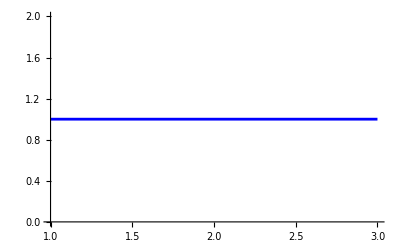

```mathematica
plotvexact=Plot[v[x]/.s,{x,xmin,xmax},PlotStyle->Blue]
```

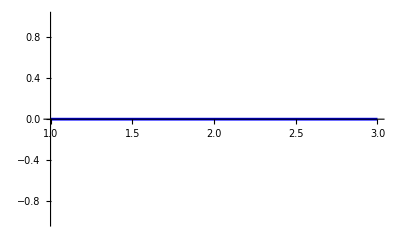

```mathematica
plotwexact=Plot[w[x]/.s,{x,xmin,xmax},PlotStyle->Blue]
```

```mathematica
plotσexact=Plot[σ[x]/.s,{x,xmin,xmax},PlotStyle->Blue]
```

-Graphics-

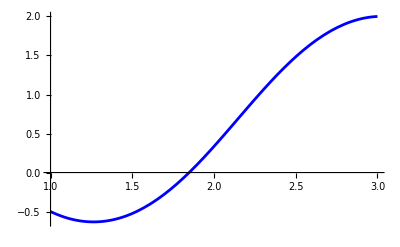

```mathematica
plotψexact=Plot[ψ[x]/.s,{x,xmin,xmax},PlotStyle->Blue]
```

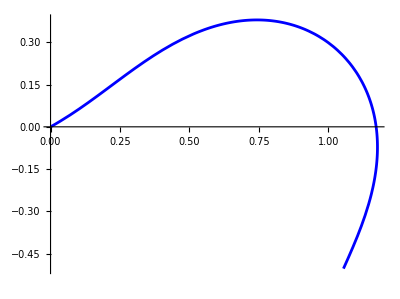

```mathematica
plotXexact=ParametricPlot[{X1[x],X2[x]}/.s,{x,xmin,xmax},PlotStyle->Blue]
```

```mathematica
(*check FE solution*)
```

```mathematica
(*check v*)
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/steady_state/flow/lagrangian_approach/one_dimension/solution/nodal_values/v.csv"];
t=Table[{t[[i,4]],t[[i,1]]},{i,2,Length[t]}]
```

{{3.,1.},{2.9,1.},{2.8,1.},{2.7,1.},{2.6,1.},{2.5,1.},{2.4,1.},{2.3,1.},{2.2,1.},{2.1,1.},{2.,1.},{1.9,1.},{1.8,1.},{1.7,1.},{1.6,1.},{1.5,1.},{1.4,1.},{1.3,1.},{1.2,1.},{1.1,1.},{1.,1.}}

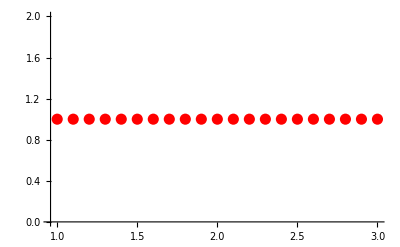

```mathematica
plotvnum=ListPlot[t,PlotRange->Full,PlotStyle->{Red,Opacity[1],PointSize->0.02}]
```

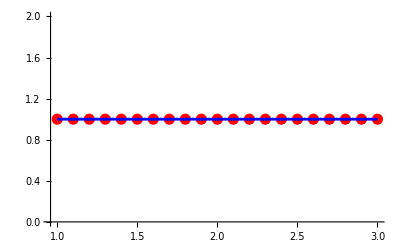

```mathematica
Show[plotvnum,plotvexact]
```

```mathematica
(*check w*)
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/steady_state/flow/lagrangian_approach/one_dimension/solution/nodal_values/w.csv"];
t=Table[{t[[i,2]],t[[i,1]]},{i,2,Length[t]}]
```

{{3.,0.},{2.9,0.},{2.8,0.},{2.7,0.},{2.6,0.},{2.5,0.},{2.4,0.},{2.3,0.},{2.2,0.},{2.1,0.},{2.,0.},{1.9,0.},{1.8,0.},{1.7,0.},{1.6,0.},{1.5,0.},{1.4,0.},{1.3,0.},{1.2,0.},{1.1,0.},{1.,0.}}

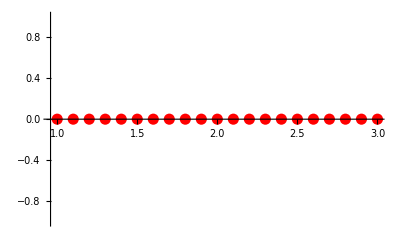

```mathematica
plotwnum=ListPlot[t,PlotRange->Full,PlotStyle->{Red,Opacity[1],PointSize->0.02}]
```

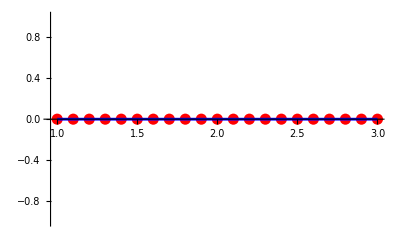

```mathematica
Show[plotwnum,plotwexact]
```

```mathematica
(*check sigma*)
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/steady_state/flow/lagrangian_approach/one_dimension/solution/nodal_values/sigma.csv"];
t=Table[{t[[i,2]],t[[i,1]]},{i,2,Length[t]}]
```

{{3.,0.},{2.9,-6.04775×10^-20},{2.8,5.96715×10^-19},{2.7,-7.16925×10^-19},{2.6,2.01944×10^-19},{2.5,-9.05899×10^-21},{2.4,2.66253×10^-20},{2.3,-1.38556×10^-19},{2.2,-4.81252×10^-19},{2.1,2.72625×10^-19},{2.,4.93322×10^-19},{1.9,-1.36647×10^-19},{1.8,-2.48816×10^-19},{1.7,5.57596×10^-19},{1.6,-5.2725×10^-19},{1.5,3.41106×10^-19},{1.4,-1.73732×10^-19},{1.3,6.90118×10^-20},{1.2,-1.29867×10^-19},{1.1,3.25924×10^-19},{1.,-4.47166×10^-19}}

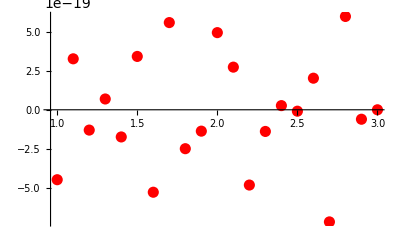

```mathematica
plotσnum=ListPlot[t,PlotRange->Full,PlotStyle->{Red,Opacity[1],PointSize->0.02}]
```

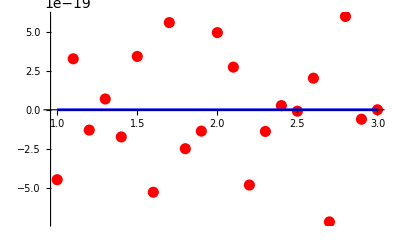

```mathematica
Show[plotσnum,plotσexact]
```

```mathematica
(*check ψ*)
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/steady_state/flow/lagrangian_approach/one_dimension/solution/nodal_values/psi.csv"];
t=Table[{t[[i,2]],t[[i,1]]},{i,2,Length[t]}]
```

{{3.,2.},{2.9,1.96965},{2.8,1.9012},{2.7,1.79553},{2.6,1.65432},{2.5,1.48045},{2.4,1.2783},{2.3,1.05404},{2.2,0.815519},{2.1,0.57184},{2.,0.332598},{1.9,0.106963},{1.8,-0.097097},{1.7,-0.273291},{1.6,-0.41709},{1.5,-0.525526},{1.4,-0.596835},{1.3,-0.63009},{1.2,-0.624927},{1.1,-0.581398},{1.,-0.5}}

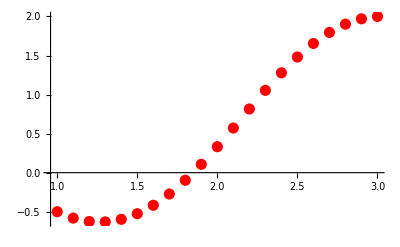

```mathematica
plotψnum=ListPlot[t,PlotRange->Full,PlotStyle->{Red,Opacity[1],PointSize->0.02}]
```

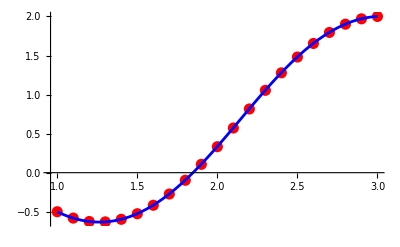

```mathematica
Show[plotψnum,plotψexact]
```

```mathematica
(*check X*)
```

```mathematica
tX=Import["/Users/michelecastellana/Documents/finite_elements/steady_state/flow/lagrangian_approach/one_dimension/solution/nodal_values/X.csv"];
tX=Table[{tX[[i,1]],tX[[i,2]]},{i,2,Length[tX]}]
```

{{1.05689,-0.502649},{1.09747,-0.411256},{1.13348,-0.317977},{1.16123,-0.221934},{1.17692,-0.123223},{1.1769,-0.0232985},{1.15817,0.0748277},{1.11906,0.166725},{1.05987,0.24715},{0.983145,0.311054},{0.893328,0.354692},{0.795843,0.376401},{0.695948,0.376771},{0.597765,0.358209},{0.503778,0.324205},{0.414805,0.278622},{0.330272,0.225221},{0.248641,0.167465},{0.167827,0.108566},{0.0856061,0.0516554},{0.,0.}}

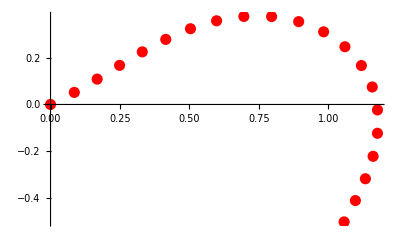

```mathematica
plotXnum=ListPlot[tX,PlotRange->Full,PlotStyle->{Red,Opacity[1],PointSize->0.02}]
```

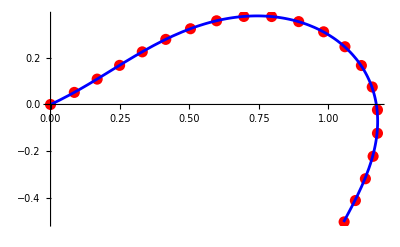

```mathematica
Show[plotXnum,plotXexact]
```